The number of pixels and the FOV are limited by the laser repetition rate, i.e., how many laser pulses can fin in a scanned line.
For a 80 MHz laser and 8 kHz scanner, there are 80 MHz/(2*8 kHz) = 5000 laser pulses.

```mathematica
μm = 10^-6;
μs=10^-6;
ms=10^-3;
ns = 10^-9;
mm=10^-3;
kHz=10^3;
Tline=62.5μs;(*Time per scanned line*)
Tlaser = 12.5ns;(*Laser pulse repetition period*)
tFPGA = 6.25ns;(*Clock of the FPGA*)
Δx=0.5μm;(*Sampling resolution*)
γ=0.8;(*filling factor that accounts for the dead time at the turning points*)
```

```mathematica
(*The parameter m is a "dwell time factor"*)
tdwell[m_]:=m*tFPGA (*Pixel dwell time*)
Npix[m_]:=γ Tline/tdwell[m](*Number of acquired pixels*)
Npp[m_]:=tdwell[m]/Tlaser(*Laser pulses per pixel*)
FFOV[m_]:=Δx*Npix[m](*Full field of view at or greater than Nyquist*)
timePerTile[m_]:=Tline*Npix[m](*Imaging time per tile. Note that the dead time at the turning points must be considered*)
```

```mathematica
header={"m","Npix","tdwell [ns]","Npp","FFOV[μm] ≤", "Time per line [μs]","Time per tile [ms]"};
TableForm[Prepend[Table[{m,Npix[m],tdwell[m]/ns,Npp[m],FFOV[m]/μm, Tline/μs,timePerTile[m]/ms},{m,10,20}],header]]
```

m | Npix | tdwell [ns] | Npp | FFOV[μm] ≤ | Time per line [μs] | Time per tile [ms]
10 | 800. | 62.5 | 5. | 400. | 62.5 | 50.
11 | 727.273 | 68.75 | 5.5 | 363.636 | 62.5 | 45.4545
12 | 666.667 | 75. | 6. | 333.333 | 62.5 | 41.6667
13 | 615.385 | 81.25 | 6.5 | 307.692 | 62.5 | 38.4615
14 | 571.429 | 87.5 | 7. | 285.714 | 62.5 | 35.7143
15 | 533.333 | 93.75 | 7.5 | 266.667 | 62.5 | 33.3333
16 | 500. | 100. | 8. | 250. | 62.5 | 31.25
17 | 470.588 | 106.25 | 8.5 | 235.294 | 62.5 | 29.4118
18 | 444.444 | 112.5 | 9. | 222.222 | 62.5 | 27.7778
19 | 421.053 | 118.75 | 9.5 | 210.526 | 62.5 | 26.3158
20 | 400. | 125. | 10. | 200. | 62.5 | 25.

```mathematica
m=20;
L=Δx*Tline/tdwell[m]; (*Full scan in μm*)
Npixfull=Npix[m]/γ;(*Full pixel number*)
L/μm (*Scan pk-pk amplitude*)
```

250.

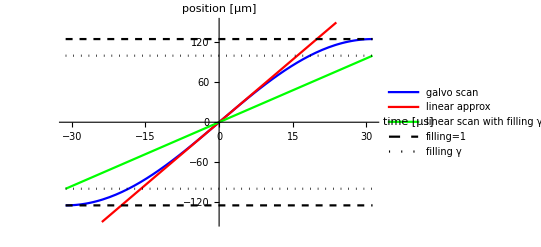

```mathematica
x[t_]:=L/2 Sin[π/Tline t](*Position of the resonant scanner vs time*)
Plot[{x[t μs]/μm,(L π)/(2Tline)t μs/μm,(γ L)/Tline t,{L/2,-L/2}/μm,γ{L/2,-L/2}/μm },{t,-Tline/2/μs,Tline/2/μs},PlotRange->{-150,150},PlotStyle->{Blue,Red,Green,{Dashed,Black},{Dotted,Black}},AxesLabel->{"time [μs]","position [μm]"} , PlotLegends->{"galvo scan","linear approx","linear scan with filling γ","filling=1","filling γ"}]
```

```mathematica
SpatialPixel[i_]:=Δx*i
SpatialPixel[Npixfull]/μm
```

250.

```mathematica
time[x_]:=Tline/π ArcSin[2/L x](*convert from spatial coordinate into time*)
```

```mathematica
Table[{pix,Re[time[SpatialPixel[pix]]]/μs},{pix,-Npixfull/2,Npixfull/2}]//TableForm;
```

```mathematica
tdwellNonlin[i_]:=time[SpatialPixel[i]]-time[SpatialPixel[i-1]]
Pulsespertpixel[i_]:=Re[tdwellNonlin[i]]/Tlaser (*Number of laser pulses that fit in the dwell time*)

(*Longer dwell times have more pulse counts. Some kind of count normalization is needed*)
PulsespertpixelNorm[i_]:=Re[tdwellNonlin[0]]/Re[tdwellNonlin[i]]
Table[{i,i-1,Re[tdwellNonlin[i]]/ns,Pulsespertpixel[i],PulsespertpixelNorm[i]},{i,Npixfull/2,-Npixfull/2+1,-1}]//TableForm;
```

```mathematica
Sum[Re[tdwellNonlin[i]]/ns,{i,-Npixfull/2+1,Npixfull/2}]
```

62500.

```mathematica
Sum[Re[tdwellNonlin[i]]/ns,{i,-Npix[m]/2+1,Npix[m]/2}]
```

36895.9

```mathematica
time[100μm]-time[-100μm]
```

0.0000368959